```mathematica
fitO := o + 1/2*y + 2*B;
fitY := 2*o + y + c*B;
fitB := o*1/2 + 2*y + B;

fitmedio := fitO * o + fitY * y + fitB * B;

dodt := o * (fitO - fitmedio);
dydt := y * (fitY - fitmedio);
dbdt := B * (fitB - fitmedio);

equilibrio = Solve[{dodt == 0 && dydt == 0 && dbdt == 0, o + y + B ==1}, {o, y, B}]
jacobiana=FullSimplify[D[{dodt,dydt,dbdt},{{o,y,B}}]];
MatrixForm[jacobiana]
```

{{o→0,y→1,B→0},{o→-1,y→2,B→0},{o→0,y→(-1+c)/c,B→1/c},{o→(2 (-5+3 c))/(-25+8 c),y→(2 (-4+c))/(-25+8 c),B→-7/(-25+8 c)},{o→2,y→0,B→-1},{o→1,y→0,B→0},{o→0,y→0,B→1}}

(-B^2-3 o^2+o (2-5 y)+1/2 (1-2 y) y-B (-2+5 o+(2+c) y) | -1/2 o (-1+2 B (2+c)+5 o+4 y) | -1/2 o (-4+4 B+5 o+2 (2+c) y)
-1/2 y (-4+5 B+4 o+5 y) | -B^2-o^2+o (2-5 y)+(2-3 y) y+B (c-(5 o)/2-4 y-2 c y) | y (-2 B+c-(5 o)/2-2 y-c y)
-1/2 B (-1+5 B+4 o+5 y) | -1/2 B (-4+2 B (2+c)+5 o+4 y) | 1/2 (-6 B^2+o+4 y-(2 o+y) (o+2 y)-2 B (-2+5 o+2 (2+c) y)))

```mathematica
equilibrio[[1]]
mat1=jacobiana/. equilibrio[[1]];
autovalores1=Eigenvalues[mat1]
Resolve[Exists[{c},c <=1 && c >= 1&& Max[Re[autovalores1]]<0]]
```

{o→1,y→0,B→0}

{-1,-1/2,c}

False

```mathematica
equilibrio[[2]]
mat2=jacobiana/. equilibrio[[2]];
autovalores2=Eigenvalues[mat2]
Resolve[Exists[{c},c <=1 &&c >= 0&& Max[Re[autovalores2]]<0]]
```

{o→0,y→0,B→1}

{-1,1,-c}

False

```mathematica
equilibrio[[4]]
mat4=jacobiana/. equilibrio[[4]];
autovalores4=Eigenvalues[mat4]
Resolve[Exists[{c},c <=1 &&c >= 0&& Max[Re[autovalores4]]<0]]
```

{o→0,y→1,B→0}

{-1,1,-1/2}

False

```mathematica
equilibrio[[5]]
mat5=jacobiana/. equilibrio[[5]];
autovalores5=Eigenvalues[mat5]
Resolve[Exists[{c},c <=1 && c >= 0&&-1+c != 0 && 1 - c != 0&& 0<=c/(-1+c) <=1&&0<=1/(1-c)<=1 && Max[Re[autovalores5]]<0]]
```

{o→0,y→c/(-1+c),B→1/(1-c)}

{(-2-3 c)/(2 (-1+c)),-c/(-1+c),-(-1+2 c)/(-1+c)}

False

```mathematica
equilibrio[[6]]
mat6=jacobiana/. equilibrio[[6]];
autovalores6=Eigenvalues[mat6]
Resolve[Exists[{c},c <=1 && 1-2 c!= 0 && -1+2 c != 0&& 0<=1/(1-2 c) <=1&&0<=(2 c)/(-1+2 c)<=1 && Max[Re[autovalores6]]<0]]
```

{o→1/(1-2 c),y→(2 c)/(-1+2 c),B→0}

{-(-1+c)/(-1+2 c),c/(-1+2 c),(1+6 c)/(2 (-1+2 c))}

False

```mathematica
equilibrio[[7]]
mat7=jacobiana/. equilibrio[[7]];
autovalores7=Eigenvalues[mat7]
Resolve[Exists[{c},c <=1 && c >= 0&& 7+18 c!= 0 && 0<=(2 (2+3 c))/(7+18 c) <=1&&0<=(2 (1+3 c))/(7+18 c)<=1 && 0<= (1+6 c)/(7+18 c) <=1 && Max[Re[autovalores7]]<0]]
```

{o→(2 (2+3 c))/(7+18 c),y→(2 (1+3 c))/(7+18 c),B→(1+6 c)/(7+18 c)}

{-(7 (7+39 c+54 c^2))/(7+18 c)^2,(-21 c-54 c^2-√(-392-6132 c-35667 c^2-99036 c^3-133164 c^4-69984 c^5))/(2 (7+18 c)^2),(-21 c-54 c^2+√(-392-6132 c-35667 c^2-99036 c^3-133164 c^4-69984 c^5))/(2 (7+18 c)^2)}

True

```mathematica
Reduce[c <=1 && c >= 0&& 7+18 c!= 0 && 0<=(2 (2+3 c))/(7+18 c) <=1&&0<=(2 (1+3 c))/(7+18 c)<=1 && 0<= (1+6 c)/(7+18 c) <=1 && Max[Re[autovalores7]]<0, c]
```

0<c≤1

```mathematica
fitO[o_,y_,B_]:=o+1/2*y+2*B;
fitY[o_,y_,B_,c_]:=2*o+y+c*B;
fitB[o_,y_,B_]:=o*1/2+2*y+B;

fitmedio[o_,y_,B_,c_]:=fitO[o,y,B]*o+fitY[o,y,B,c]*y+fitB[o,y,B]*B;

dodt[o_,y_,B_,c_]:=o*(fitO[o,y,B]-fitmedio[o,y,B,c]);

dydt[o_,y_,B_,c_]:=y*(fitY[o,y,B,c]-fitmedio[o,y,B,c]);

dbdt[o_,y_,B_,c_]:=B*(fitB[o,y,B]-fitmedio[o,y,B,c]);
```

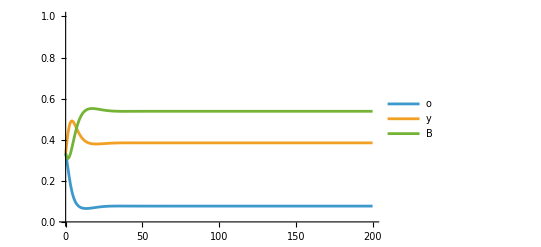

```mathematica
c = 1.5;
sol1=NDSolve[{o'[t]==dodt[o[t],y[t],B[t],c],y'[t]==dydt[o[t],y[t],B[t],c],B'[t]==dbdt[o[t],y[t],B[t],c],o[0]==0.333,y[0]==0.333,B[0]==0.334},{o,y,B},{t,0,200}];
Plot[Evaluate[{o[t],y[t],B[t]}/. sol1],{t,0,200},PlotLegends->{"o","y","B"},PlotRange->{0,1}]
```